# octet.experiment.rencon1.figure.lambda-1.00.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.paper.mine.fch\octet.experiment.rencon1.figure.lambda-1.00.nb

this nb is to record the octet ge gm experiment data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

## nucleon`ge`light-sea

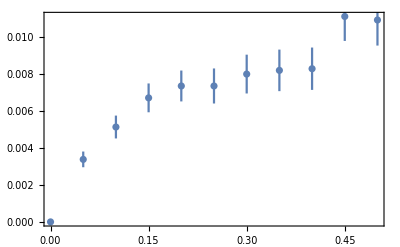
```mathematica
fig`exp`nucleon`ge`lightsea=
-Graphics-/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

## fig`calc`nucleon`ge`u

```mathematica
fig`calc`nucleon`ge`u=
-Graphics-;
```

## fig`calc`nucleon`ge`d

```mathematica
fig`calc`nucleon`ge`d=
-Graphics-;
```

## fig`comparison`ge`u

```mathematica
fig`comparison`ge`u=Show[
{fig`calc`nucleon`ge`u,fig`exp`nucleon`ge`lightsea},
AxesOrigin->{0,0},
PlotRange->{Automatic,All},
PlotRangePadding->{Automatic,Automatic},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## fig`comparison`ge`d

```mathematica
fig`comparison`ge`d=Show[
{fig`calc`nucleon`ge`d,fig`exp`nucleon`ge`lightsea},
AxesOrigin->{0,0},
PlotRange->{Automatic,All},
PlotRangePadding->{Automatic,Automatic},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## nucleon`ge`strange

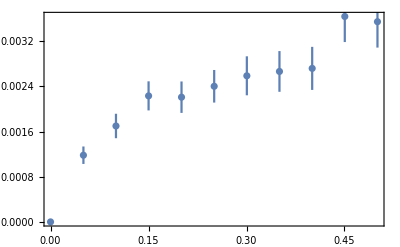
```mathematica
fig`exp`nucleon`ge`s=
-Graphics-/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

## fig`calc`nucleon`ge`s

```mathematica
fig`calc`nucleon`ge`s=
-Graphics-;
```

```mathematica
fig`comparison`ge`s=Show[
{fig`exp`nucleon`ge`s,fig`calc`nucleon`ge`s},
AxesOrigin->{0,0},
PlotRange->{Automatic,All},
PlotRangePadding->{Automatic,Automatic},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## nucleon`gm`lightsea

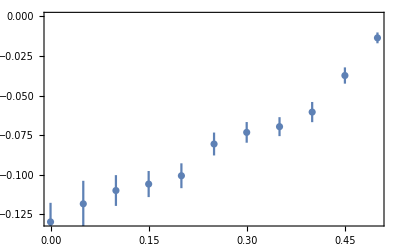
```mathematica
fig`exp`nucleon`gm`lightsea=
-Graphics-/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

## fig`calc`nucleon`gm`u

```mathematica
fig`calc`nucleon`gm`u=
-Graphics-;
```

## fig`calc`nucleon`gm`d

```mathematica
fig`calc`nucleon`gm`d=
-Graphics-;
```

## fig`comparison`gm`u

```mathematica
fig`comparison`gm`u=Show[
{fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`u},
AxesOrigin->{0,0},
PlotRange->{Automatic,All},
PlotRangePadding->{Automatic,Scaled[.03]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## fig`comparison`gm`d

```mathematica
fig`comparison`gm`d=Show[
{fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`d},
AxesOrigin->{0,0},
PlotRange->{Automatic,All},
PlotRangePadding->{Automatic,Scaled[.03]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## nucleon`gm`strange

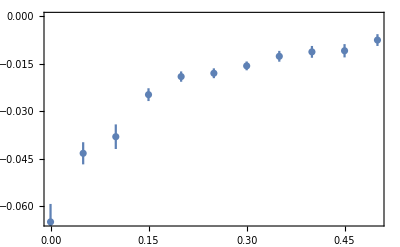
```mathematica
fig`exp`nucleon`gm`s=-Graphics-/.{RGBColor[0.368417,0.506779,0.709798]->Blue};
```

## fig`calc`nucleon`gm`s

```mathematica
fig`calc`nucleon`gm`s=
-Graphics-;
```

```mathematica
fig`comparison`gm`s=Show[
{fig`exp`nucleon`gm`s,fig`calc`nucleon`gm`s},
AxesOrigin->{0,0},
PlotRange->{Automatic,Automatic},
PlotRangePadding->{Automatic,Scaled[.03]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## paper`show

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

u

```mathematica
fig`sea`u=Labeled[
GraphicsGrid[
{{fig`comparison`ge`u/.(ImagePadding->_)->(ImagePadding->All)(*fig`comparison`ge`u*),fig`comparison`gm`u}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea u"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]/.{AbsoluteThickness[_]-> AbsoluteThickness[0.5],PointSize[_]->PointSize[0.02]}
```

-Graphics-sea u

d

```mathematica
fig`sea`d=Labeled[
GraphicsGrid[
{{fig`comparison`ge`d/.(ImagePadding->_)->(ImagePadding->All)(*fig`comparison`ge`u*),fig`comparison`gm`d}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea d"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]/.{AbsoluteThickness[_]-> AbsoluteThickness[0.5],PointSize[_]->PointSize[0.02]}
```

-Graphics-sea d

s

```mathematica
fig`sea`s=Labeled[
GraphicsGrid[
{{fig`comparison`ge`s,fig`comparison`gm`s}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea s"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]/.{AbsoluteThickness[_]-> AbsoluteThickness[0.5],PointSize[_]->PointSize[0.02]}
```

-Graphics-sea s

export

```mathematica
SetDirectory["C:\\Users\\Tom\\Desktop"];
```

```mathematica
Export["fig.sea.u.eps",fig`sea`u];
Export["fig.sea.d.eps",fig`sea`d];
Export["fig.sea.s.eps",fig`sea`s];
```